```mathematica
Artificial Intelligence HW 3

Data Import
raw=OpenRead["/Users/kaien/Desktop/hw3/reviews.csv"];
input=Map[StringSplit[#,"|"]&,ReadList[raw,String]];


Data Preprocessing

(* make balanced training set: 1000 positive samples, 1000 negative samples *)
SampleSize = 2000;
pList = List[];
nList = List[];
pCount = 0;
nCount = 0;
i = 2;
While[True, 
If[pCount >= SampleSize/2 && nCount >= SampleSize/2, Break[]];
If[input[[i, 1]] == "positive", AppendTo[pList, input[[i]]]; pCount++;, AppendTo[nList, input[[i]]]; nCount++;];
i++;
]

(* zigzag *)
input = List[];
For[i = 1, i ≤ SampleSize/2, i++,
AppendTo[input, pList[[i]]];
AppendTo[input, nList[[i]]];
]

(* Shuffling trainsets *)
input = RandomSample[input];

textSet1={}; (* Paragraph *)
textSet2={}; (* Uni-gram *)
textSet3={};(* Bi-gram *)
textSet4={};(* Uni-gram + Bi-gram *)
textSet5={}; (* Uni-gram + Stop Words *)
textSet6={}; (* Bi-gram + Stop Words *)
textSet7={}; (* Uni-gram + Bi-gram + Stop Words *)
textSet8={}; (* Uni-gram + Bi-gram + Tri-gram *)
labelSet={}; 

(* Data Preprocessing for 8 different ways *)
For[i=1,i≤SampleSize,i++,parsedText=StringSplit[input[[{i},2]],Except[Characters["QWERTYUIOPASDFGHJKLZXCVBNMqwertyuiopasdfghjklzxcvbnm'"]]..];
finalText=Flatten[Map[ToLowerCase,parsedText]];
noStopfinalText=DeleteStopwords[Flatten[finalText]];

bigrams=Partition[finalText,2,1];
trigrams =Partition[finalText,3,1];
bigramsStopwords=Partition[noStopfinalText,2,1];

For[j = 1, j ≤ Length[bigrams], j++, 
bigrams[[j]] = bigrams[[j, 1]]  bigrams[[j, 2]];
];
For[k = 1, k ≤ Length[bigramsStopwords], k++, 
bigramsStopwords[[k]] = bigramsStopwords[[k, 1]]  bigramsStopwords[[k, 2]];
];
For[l = 1, l ≤ Length[trigrams], l++, 
trigrams[[l]] = trigrams[[l, 1]]  trigrams[[l, 2]]trigrams[[l,3]];
];

AppendTo[textSet1, input[[i, 2]]];
AppendTo[textSet2, finalText]; 
AppendTo[textSet3, bigrams];
AppendTo[textSet4,Join[finalText, bigrams]];
AppendTo[textSet5, noStopfinalText]; 
AppendTo[textSet6, bigramsStopwords];
AppendTo[textSet7,Join[noStopfinalText, bigramsStopwords]];
AppendTo[textSet8,Join[Join[finalText, bigrams], trigrams]];
AppendTo[labelSet,input[[i,1]]];
]

Measure the best way for the data preprocessing
(* Measure the best way for the data preprocessing *)
measureSize = SampleSize;
testText1=Take[textSet1[[;;measureSize]],{1,-1,5}];
trainText1=Drop[textSet1[[;;measureSize]],{1,-1,5}];
testText2=Take[textSet2[[;;measureSize]],{1,-1,5}];
trainText2=Drop[textSet2[[;;measureSize]],{1,-1,5}];
testText3=Take[textSet3[[;;measureSize]],{1,-1,5}];
trainText3=Drop[textSet3[[;;measureSize]],{1,-1,5}];
testText4=Take[textSet4[[;;measureSize]],{1,-1,5}];
trainText4=Drop[textSet4[[;;measureSize]],{1,-1,5}];
testText5=Take[textSet5[[;;measureSize]],{1,-1,5}];
trainText5=Drop[textSet5[[;;measureSize]],{1,-1,5}];
testText6=Take[textSet6[[;;measureSize]],{1,-1,5}];
trainText6=Drop[textSet6[[;;measureSize]],{1,-1,5}];
testText7=Take[textSet7[[;;measureSize]],{1,-1,5}];
trainText7=Drop[textSet7[[;;measureSize]],{1,-1,5}];
testText8=Take[textSet8[[;;measureSize]],{1,-1,5}];
trainText8=Drop[textSet8[[;;measureSize]],{1,-1,5}];
testLabel=Take[labelSet[[;;measureSize]],{1,-1,5}];
trainLabel=Drop[labelSet[[;;measureSize]],{1,-1,5}];

c1=Classify[trainText1->trainLabel];
cm1 = ClassifierMeasurements[c1, testText1-> testLabel];
c2=Classify[trainText2->trainLabel];
cm2 = ClassifierMeasurements[c2, testText2-> testLabel];
c3=Classify[trainText3->trainLabel];
cm3= ClassifierMeasurements[c3, testText3-> testLabel];
c4=Classify[trainText4->trainLabel];
cm4 = ClassifierMeasurements[c4, testText4-> testLabel];
c5=Classify[trainText5->trainLabel];
cm5 = ClassifierMeasurements[c5, testText5-> testLabel];
c6=Classify[trainText6->trainLabel];
cm6 = ClassifierMeasurements[c6, testText6-> testLabel];
c7=Classify[trainText7->trainLabel];
cm7 = ClassifierMeasurements[c7, testText7-> testLabel];
c8=Classify[trainText8->trainLabel];
cm8 = ClassifierMeasurements[c8, testText8-> testLabel];

ListPlot[{cm1["Accuracy"],cm2["Accuracy"],cm3["Accuracy"],cm4["Accuracy"],cm5["Accuracy"],cm6["Accuracy"],cm7["Accuracy"],cm8["Accuracy"]}->{"Paragraph", "Unigram", "Bigram", "Unigram+Bigram", 
"Unigram with trimming stopwords", "Bigram with trimming stopwords", "Unigram+Bigram with trimming stopwords", "Unigram+Bigram+Trigram"}, PlotTheme->"Scientific"]

Accuracy for 8 different ways with 2000 trainset and Markov Classifier
```

-Graphics-

```mathematica
Data Classification
(* We are going to use only Unigram + Bigram for measuring each model's accuracy *)
dataSizeForModel = List[200, 400, 600, 800, 1000, 1200, 1400, 1600, 1800, 2000];


Random Forest Classifier

(* Random Forest Classifier *)
AccuracyList1 = List[];
ErrorRateList1 = List[];
RecallList1 = List[];
PrecisionList1 = List[];
SpecificityList1 = List[];
FalseAlarmRateList1 = List[];
For[dataSizeIndex = 1, dataSizeIndex ≤ Length[dataSizeForModel], dataSizeIndex++,
testText=Take[textSet4[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
trainText=Drop[textSet4[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
testLabel=Take[labelSet[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
trainLabel=Drop[labelSet[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
c1=Classify[trainText->trainLabel, Method->{"RandomForest", "TreeNumber"-> 100}];
cm1 = ClassifierMeasurements[c1, testText-> testLabel];
n = cm1["ConfusionMatrix"];
AppendTo[AccuracyList1, cm1["Accuracy"]];
AppendTo[ErrorRateList1, (n[[1,1]]+n[[1,2]])/(n[[1,1]]+n[[1,2]]+n[[2,1]]+n[[2,2]])];
AppendTo[RecallList1, n[[2,2]]/(n[[1,1]]+n[[2,2]])];
AppendTo[PrecisionList1, n[[2,2]]/(n[[1,2]]+n[[2,2]])];
AppendTo[SpecificityList1, n[[2,1]]/(n[[1,2]]+n[[2,1]])];
AppendTo[FalseAlarmRateList1, n[[1,2]]/(n[[1,2]]+n[[2,1]])];
]



Neural Network Classifier

(* Neural Network Classifier *)
AccuracyList2 = List[];
ErrorRateList2 = List[];
RecallList2 = List[];
PrecisionList2 = List[];
SpecificityList2 = List[];
FalseAlarmRateList2 = List[];
For[dataSizeIndex = 1, dataSizeIndex ≤ Length[dataSizeForModel], dataSizeIndex++,
testText=Take[textSet4[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
trainText=Drop[textSet4[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
testLabel=Take[labelSet[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
trainLabel=Drop[labelSet[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
c2=Classify[trainText->trainLabel, Method->"NeuralNetwork"];
cm2 = ClassifierMeasurements[c2, testText-> testLabel];
n = cm2["ConfusionMatrix"];
AppendTo[AccuracyList2, cm2["Accuracy"]];
AppendTo[ErrorRateList2, (n[[1,1]]+n[[1,2]])/(n[[1,1]]+n[[1,2]]+n[[2,1]]+n[[2,2]])];
AppendTo[RecallList2, n[[2,2]]/(n[[1,1]]+n[[2,2]])];
AppendTo[PrecisionList2, n[[2,2]]/(n[[1,2]]+n[[2,2]])];
AppendTo[SpecificityList2, n[[2,1]]/(n[[1,2]]+n[[2,1]])];
AppendTo[FalseAlarmRateList2, n[[1,2]]/(n[[1,2]]+n[[2,1]])];
]


Support Vector Machine Classifier

(* Support Vector Machine Classifier *)
AccuracyList3 = List[];
ErrorRateList3 = List[];
RecallList3 = List[];
PrecisionList3 = List[];
SpecificityList3 = List[];
FalseAlarmRateList3 = List[];
For[dataSizeIndex = 1, dataSizeIndex ≤ Length[dataSizeForModel], dataSizeIndex++,
testText=Take[textSet4[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
trainText=Drop[textSet4[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
testLabel=Take[labelSet[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
trainLabel=Drop[labelSet[[;;dataSizeForModel[[dataSizeIndex]]-1]],{1,-1,5}];
c3=Classify[trainText->trainLabel, Method->"SupportVectorMachine"];
cm3 = ClassifierMeasurements[c3, testText-> testLabel];
n = cm3["ConfusionMatrix"];
AppendTo[AccuracyList3, cm3["Accuracy"]];
AppendTo[ErrorRateList3, (n[[1,1]]+n[[1,2]])/(n[[1,1]]+n[[1,2]]+n[[2,1]]+n[[2,2]])];
AppendTo[RecallList3, n[[2,2]]/(n[[1,1]]+n[[2,2]])];
AppendTo[PrecisionList3, n[[2,2]]/(n[[1,2]]+n[[2,2]])];
AppendTo[SpecificityList3, n[[2,1]]/(n[[1,2]]+n[[2,1]])];
AppendTo[FalseAlarmRateList3, n[[1,2]]/(n[[1,2]]+n[[2,1]])];
]
```

Data Visualization

Forest Random Result

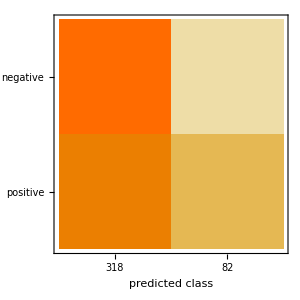

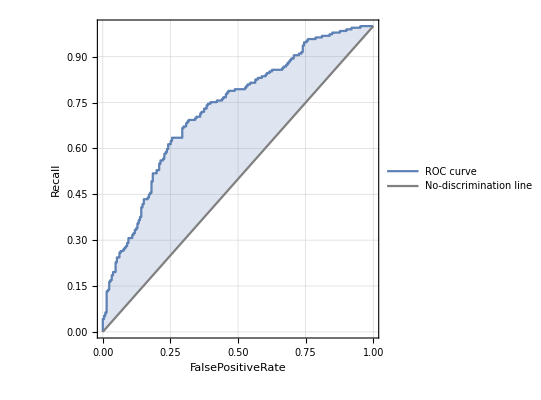
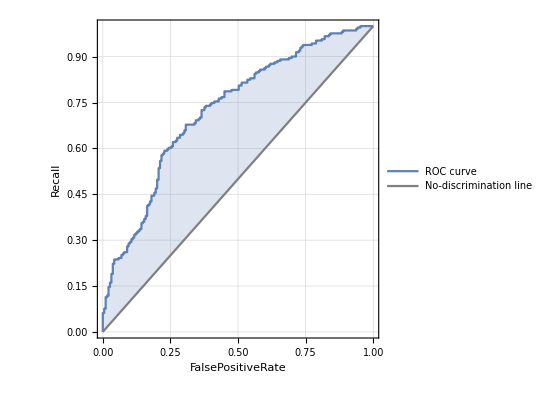
<|negative→-Graphics-,positive→-Graphics-|>

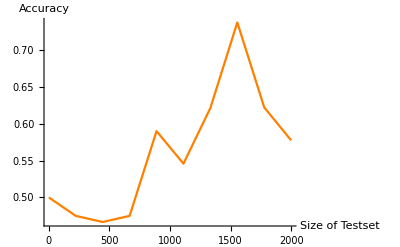

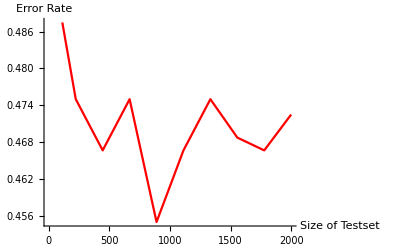

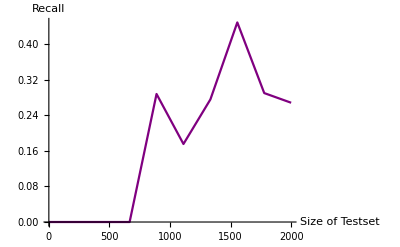

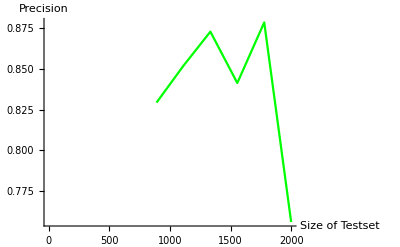

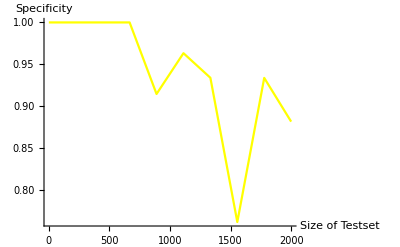

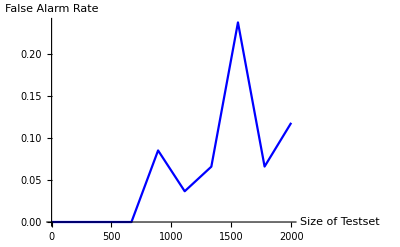

Network Neural Result

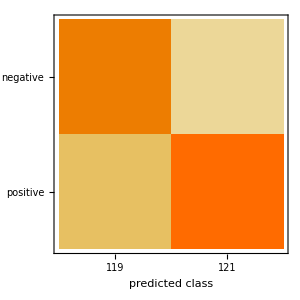

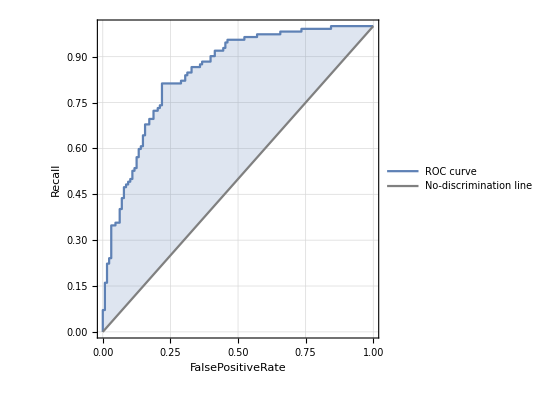
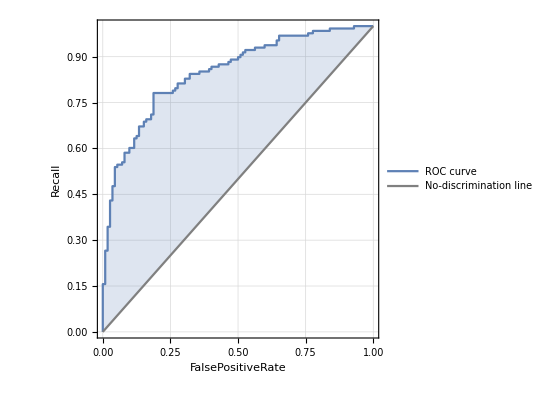
<|negative→-Graphics-,positive→-Graphics-|>

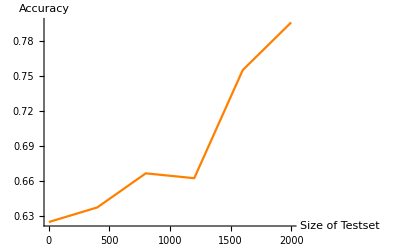

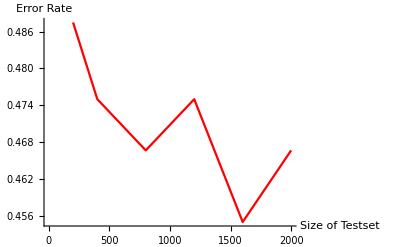

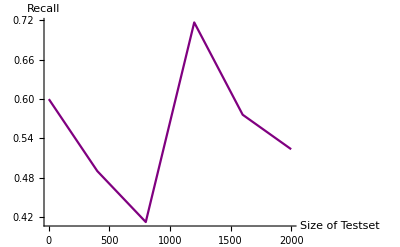

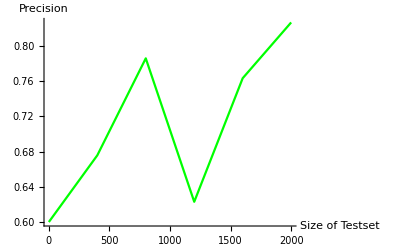

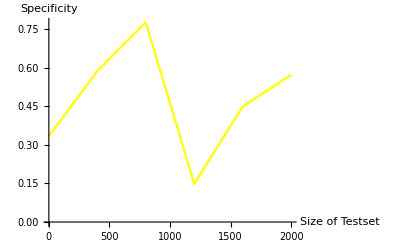

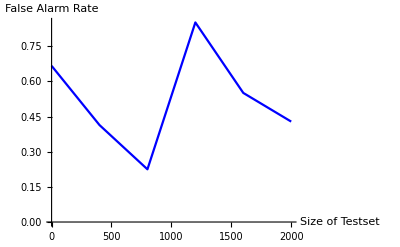

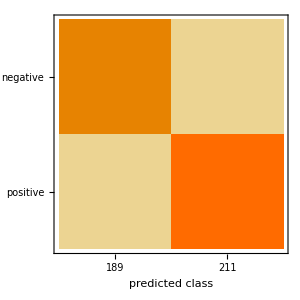

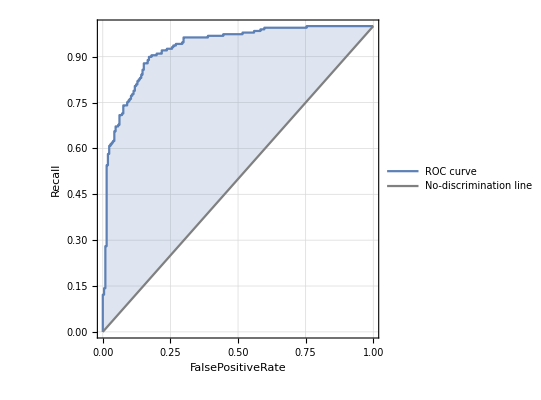
<|negative→-Graphics-,positive→-Graphics-|>

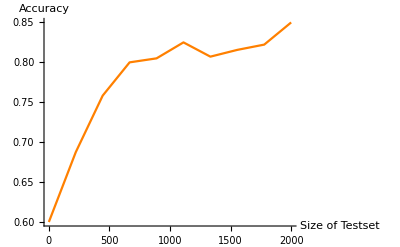

-Graphics-

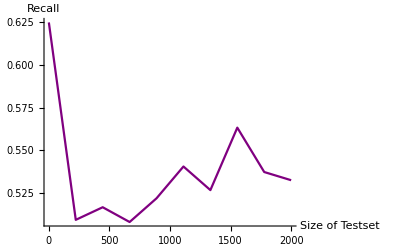

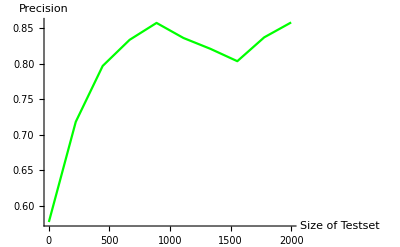

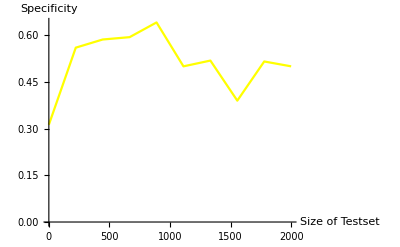

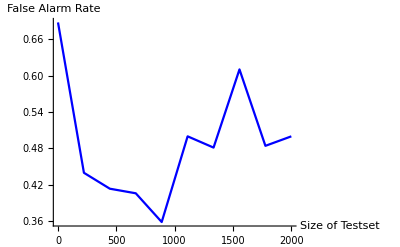

Comparison Performance

-Graphics-

```mathematica
Data Visualization

Random Forest Result

(* ConfusionMatrix Plot*)
cm1["ConfusionMatrixPlot"]
(* ROC Curve *)
cm1["ROCCurve"]
(* Accuracy Graph according to the size of testset *)
ListLinePlot[AccuracyList1 , AxesLabel->{"Size of Testset","Accuracy"}, PlotStyle->Orange, DataRange->dataSizeForModel[[-1]]]
(* Error Rate Graph *)
ListLinePlot[ErrorRateList1 , AxesLabel->{"Size of Testset","Error Rate"}, PlotStyle->Red, DataRange->dataSizeForModel[[-1]]]
(* Recall Graph *)
ListLinePlot[RecallList1 , AxesLabel->{"Size of Testset","Recall"}, PlotStyle->Purple, DataRange->dataSizeForModel[[-1]]]
(* Precision Graph *)
ListLinePlot[PrecisionList1 , AxesLabel->{"Size of Testset","Precision"}, PlotStyle->Green, DataRange->dataSizeForModel[[-1]]]
(* Specificity Graph *)
ListLinePlot[SpecificityList1 , AxesLabel->{"Size of Testset","Specificity"}, PlotStyle->Yellow, DataRange->dataSizeForModel[[-1]]]
(* False Alarm Rate Graph *)
ListLinePlot[FalseAlarmRateList1 , AxesLabel->{"Size of Testset","False Alarm Rate"}, PlotStyle->Blue, DataRange->dataSizeForModel[[-1]]]

Neural Network Result

(* ConfusionMatrix Plot*)
cm2["ConfusionMatrixPlot"]
(* ROC Curve *)
cm2["ROCCurve"]
(* Accuracy Graph according to the size of testset *)
ListLinePlot[AccuracyList2 , AxesLabel->{"Size of Testset","Accuracy"}, PlotStyle->Orange, DataRange->dataSizeForModel[[-1]]]
(* Error Rate Graph *)
ListLinePlot[ErrorRateList2 , AxesLabel->{"Size of Testset","Error Rate"}, PlotStyle->Red, DataRange->dataSizeForModel[[-1]]]
(* Recall Graph *)
ListLinePlot[RecallList2, AxesLabel->{"Size of Testset","Recall"}, PlotStyle->Purple, DataRange->dataSizeForModel[[-1]]]
(* Precision Graph *)
ListLinePlot[PrecisionList2 , AxesLabel->{"Size of Testset","Precision"}, PlotStyle->Green, DataRange->dataSizeForModel[[-1]]]
(* Specificity Graph *)
ListLinePlot[SpecificityList2 , AxesLabel->{"Size of Testset","Specificity"}, PlotStyle->Yellow, DataRange->dataSizeForModel[[-1]]]
(* False Alarm Rate Graph *)
ListLinePlot[FalseAlarmRateList2 , AxesLabel->{"Size of Testset","False Alarm Rate"}, PlotStyle->Blue, DataRange->dataSizeForModel[[-1]]]

Support Vector Machine Result

(* ConfusionMatrix Plot*)
cm3["ConfusionMatrixPlot"]
(* ROC Curve *)
cm3["ROCCurve"]
(* Accuracy Graph according to the size of testset *)
ListLinePlot[AccuracyList3 , AxesLabel->{"Size of Testset","Accuracy"}, PlotStyle->Orange, DataRange->dataSizeForModel[[-1]]]
(* Error Rate Graph *)
ListLinePlot[ErrorRateList3 , AxesLabel->{"Size of Testset","Error Rate"}, PlotStyle->Red, DataRange->dataSizeForModel[[-1]]]
(* Recall Graph *)
ListLinePlot[RecallList3, AxesLabel->{"Size of Testset","Recall"}, PlotStyle->Purple, DataRange->dataSizeForModel[[-1]]]
(* Precision Graph *)
ListLinePlot[PrecisionList3 , AxesLabel->{"Size of Testset","Precision"}, PlotStyle->Green, DataRange->dataSizeForModel[[-1]]]
(* Specificity Graph *)
ListLinePlot[SpecificityList3 , AxesLabel->{"Size of Testset","Specificity"}, PlotStyle->Yellow, DataRange->dataSizeForModel[[-1]]]
(* False Alarm Rate Graph *)
ListLinePlot[FalseAlarmRateList3 , AxesLabel->{"Size of Testset","False Alarm Rate"}, PlotStyle->Blue, DataRange->dataSizeForModel[[-1]]]

Performance  Comparison
ListPlot[{cm1["Accuracy"], cm2["Accuracy"], cm3["Accuracy"]}->{"Random Forest","Neural Network","Support Vector Machine"}, AxesLabel->{"Type of Model","Accuracy"}, PlotStyle->Orange]
```

```mathematica
ClassifierInformation[c1]
ClassifierInformation[c2]
ClassifierInformation[c3]
```

Classifier information
Method | Random forest
Number of classes | 2
Number of features | 1
Number of training examples | 1599
Number of trees | 100

Classifier information
Method | Neural network
Number of classes | 2
Number of features | 1
Number of training examples | 959
L1 regularization coefficient | 0
L2 regularization coefficient | 0.1
Number of hidden layers | 2
Hidden nodes | ,,28742874
Hidden layer activation functions | ,,Rectified LinearRectified Linear
CostFunction | Cost Function

Classifier information
Method | Support vector machine
Number of classes | 2
Number of features | 1
Number of training examples | 1599
Number of extracted features | 1598
Kernel type | Radial basis function
Soft margin parameter | 4096.